Real f(ω)
parameters: SUS 304

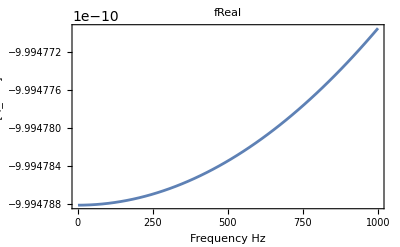

```mathematica
fRe=6/b^3((2χ)/ω)^(3/2)1/((Cos[ξd]Cosh[ξd])^2+(Sin[ξd]Sinh[ξd])^2)(Cos[ξd]Cosh[ξd](Sin[ξ]Cosh[ξ]-Cos[ξ]Sinh[ξ]-2 ξ Sin[ξ]Sinh[ξ])-Sin[ξd]Sinh[ξd](Sin[ξ]Cosh[ξ]+Cos[ξ]Sinh[ξ]-2 ξ Cos[ξ]Cosh[ξ]))/.
{ξ->b/2 √(ω/(2χ)),ξd->bd/2 √(ω/(2χ)),χ->λ/(ρ Cv)}/.
{ρ->7.93 10^3,Cv->460,λ->16.3,α->16.3 10^-8,ω->2π f,χ->4.47,b->2 10^-3,bd->3 10^-3};
Plot[fRe,{f,1,1000},PlotLabel->fReal, Frame->True,FrameLabel->{Frequency(Hz),f_real}]
```

fRe 1st term

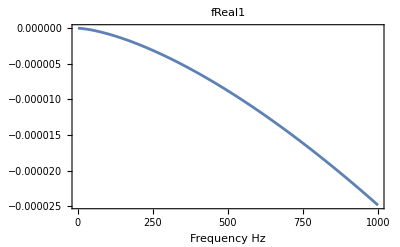

```mathematica
fRe1=Cos[ξd]Cosh[ξd](Sin[ξ]Cosh[ξ]-Cos[ξ]Sinh[ξ]-2 ξ Sin[ξ]Sinh[ξ])/.
{ξ->b/2 √(ω/(2χ)),ξd->bd/2 √(ω/(2χ)),χ->λ/(ρ Cv)}/.
{ρ->7.93 10^3,Cv->460,λ->16.3,α->16.3 10^-8,ω->2π f,χ->4.47,b->2 10^-3,bd->3 10^-3};
Plot[fRe1,{f,1,1000},PlotLabel->fReal1, Frame->True,FrameLabel->{Frequency(Hz),1st}]
```

fRe 2nd term

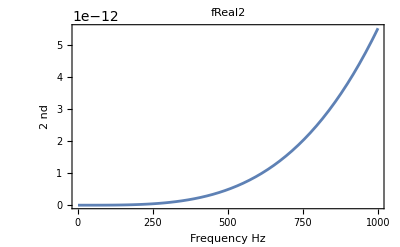

```mathematica
fRe2=Sin[ξd]Sinh[ξd](Sin[ξ]Cosh[ξ]+Cos[ξ]Sinh[ξ]-2 ξ Cos[ξ]Cosh[ξ])/.
{ξ->b/2 √(ω/(2χ)),ξd->bd/2 √(ω/(2χ)),χ->λ/(ρ Cv)}/.
{ρ->7.93 10^3,Cv->460,λ->16.3,α->16.3 10^-8,ω->2π f,χ->4.47,b->2 10^-3,bd->3 10^-3};
Plot[fRe2,{f,1,1000},PlotLabel->fReal2, Frame->True,FrameLabel->{Frequency(Hz),2nd}]
```

Sin[ξ] Cosh[ξ]

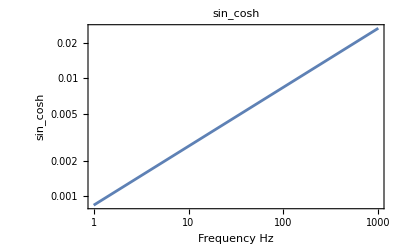

```mathematica
SCh=Sin[ξ]Cosh[ξ]/.
{ξ->b/2 √(ω/(2χ)),ξd->bd/2 √(ω/(2χ)),χ->λ/(ρ Cv)}/.
{ρ->7.93 10^3,Cv->460,λ->16.3,α->16.3 10^-8,ω->2π f,χ->4.47,b->2 10^-3,bd->3 10^-3};
SChg=LogLogPlot[SCh,{f,1,1000},PlotLabel->sin_cosh, Frame->True,FrameLabel->{Frequency(Hz),sin_cosh}]
```

Cos[ξ] Sinh[ξ]

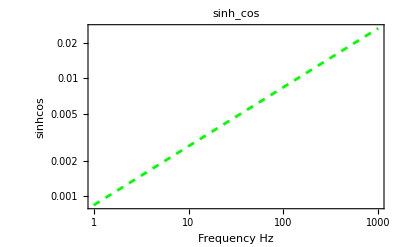

```mathematica
CSh=Cos[ξ]Sinh[ξ]/.
{ξ->b/2 √(ω/(2χ)),ξd->bd/2 √(ω/(2χ)),χ->λ/(ρ Cv)}/.
{ρ->7.93 10^3,Cv->460,λ->16.3,α->16.3 10^-8,ω->2π f,χ->4.47,b->2 10^-3,bd->3 10^-3};
CShg=LogLogPlot[CSh,{f,1,1000},PlotLabel->sinh_cos,PlotStyle->{Dashed,Green}, Frame->True,FrameLabel->{Frequency(Hz),sinhcos}]
```

2ξ Sin[ξ] Sinh[ξ]

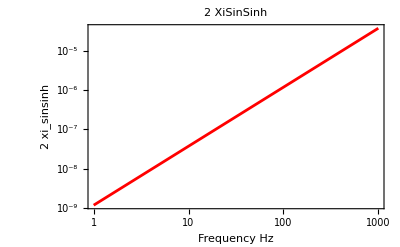

```mathematica
xSSh=2 ξ Sin[ξ]Sinh[ξ]/.
{ξ->b/2 √(ω/(2χ)),ξd->bd/2 √(ω/(2χ)),χ->λ/(ρ Cv)}/.
{ρ->7.93 10^3,Cv->460,λ->16.3,α->16.3 10^-8,ω->2π f,χ->4.47,b->2 10^-3,bd->3 10^-3};
xSShg=LogLogPlot[xSSh,{f,1,1000},PlotLabel->2XiSinSinh,PlotStyle->{Red}, Frame->True,FrameLabel->{Frequency(Hz),2xi_sinsinh}]
```

2ξ Cos[ξ] Cosh[ξ]

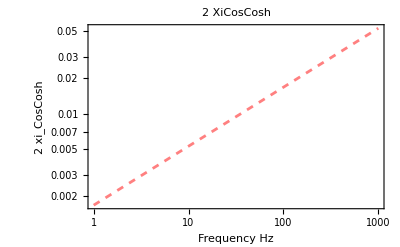

```mathematica
xCCh=2 ξ Cos[ξ]Cosh[ξ]/.
{ξ->b/2 √(ω/(2χ)),ξd->bd/2 √(ω/(2χ)),χ->λ/(ρ Cv)}/.
{ρ->7.93 10^3,Cv->460,λ->16.3,α->16.3 10^-8,ω->2π f,χ->4.47,b->2 10^-3,bd->3 10^-3};
xCChg=LogLogPlot[xCCh,{f,1,1000},PlotLabel->2XiCosCosh,PlotStyle->{Dashed,Pink}, Frame->True,FrameLabel->{Frequency(Hz),2xi_CosCosh}]
```

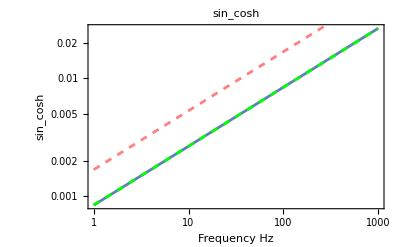

```mathematica
Show[SChg,CShg,xSShg,xCChg]
```